## Base model

```mathematica
mat={{rh-me,mh},{me,re-mh}}
```

{{-me+rh,mh},{me,-mh+re}}

```mathematica
mat//MatrixForm
```

(-me+rh | mh
me | -mh+re)

```mathematica
Eigensystem[mat]
```

{{1/2 (-me-mh+re+rh-√((me+mh-re-rh)^2-4 (-me re-mh rh+re rh))),1/2 (-me-mh+re+rh+√((me+mh-re-rh)^2-4 (-me re-mh rh+re rh)))},{{-(me-mh+re-rh+√(me^2+2 me mh+mh^2+2 me re-2 mh re+re^2-2 me rh+2 mh rh-2 re rh+rh^2))/(2 me),1},{-(me-mh+re-rh-√(me^2+2 me mh+mh^2+2 me re-2 mh re+re^2-2 me rh+2 mh rh-2 re rh+rh^2))/(2 me),1}}}

```mathematica
(*Largest eigenvalue*)
```

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

## Temporal plot

```mathematica
eq1B={D[nH[t],t]==rh*nH[t]-me*nH[t]+mh*nE[t],nH[0]==nH0}
```

{nH'[t]==mh nE[t]-me nH[t]+rh nH[t],nH[0]==nH0}

```mathematica
eq2B={D[nE[t],t]==re*nE[t]-mh*nE[t]+me*nH[t] ,nE[0]==nE0}
```

{nE'[t]==-mh nE[t]+re nE[t]+me nH[t],nE[0]==nE0}

```mathematica
sysB={eq1B,eq2B}
```

{{nH'[t]==mh nE[t]-me nH[t]+rh nH[t],nH[0]==nH0},{nE'[t]==-mh nE[t]+re nE[t]+me nH[t],nE[0]==nE0}}

```mathematica
FullSimplify[DSolve[sysB,{nH[t],nE[t]},t]]
```

{{nE[t]→(ⅇ^(-1/2 (me+mh-re-rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)) t) (-me nE0+mh nE0-2 me nH0-nE0 re+nE0 rh+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t) (me (nE0+2 nH0)-nE0 (mh-re+rh))+nE0 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t) nE0 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))/(2 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)),nH[t]→(ⅇ^(-1/2 (me+mh-re-rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)) t) (me nH0+(-1+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t)) mh (2 nE0+nH0)+nH0 (re-rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t) (-me-re+rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))))/(2 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2))}}

```mathematica
NEBase[t_,re_,rh_,me_,mh_]:=(ⅇ^(-1/2 (me+mh-re-rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)) t) (-me nE0+mh nE0-2 me nH0-nE0 re+nE0 rh+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t) (me (nE0+2 nH0)-nE0 (mh-re+rh))+nE0 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t) nE0 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))/(2 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2))
```

```mathematica
NHBase[t_,re_,rh_,me_,mh_]:=(ⅇ^(-1/2 (me+mh-re-rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)) t) (me nH0+(-1+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t)) mh (2 nE0+nH0)+nH0 (re-rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)+ⅇ^(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2) t) (-me-re+rh+√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))))/(2 √(me^2+2 me (mh+re-rh)+(mh-re+rh)^2))
```

Figure 1 panel B

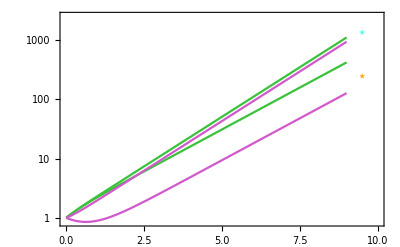

```mathematica
Show[LogPlot[{NEBase[t,1,-0.5,0.5,0.5]/.nE0->1/.nH0->1,NHBase[t,1,-0.5,0.5,0.5]/.nE0->1/.nH0->1},{t,0,9},PlotRange->{{0,10},{0,2500}},PlotStyle->{Directive[RGBColor[0.23, 0.76, 0.23]],Directive[RGBColor[0.8200000000000001, 0.35000000000000003, 0.8]]},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},Frame->True,FrameTicks->{{{{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"}},None},{Automatic,None}}],LogPlot[{NEBase[t,1,0.5,1.5,1.5]/.nE0->1/.nH0->1,NHBase[t,1,0.5,1.5,1.5]/.nE0->1/.nH0->1},{t,0,9},PlotRange->All,PlotStyle->{RGBColor[0.23, 0.76, 0.23],RGBColor[0.8200000000000001, 0.35000000000000003, 0.8]},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},Frame->True],ListPlot[{{9.5,7.2}},PlotMarkers->{Style[★,Large,RGBColor[0.33, 1., 0.92]]},PlotStyle->PointSize[Large]],ListPlot[{{9.5,5.5}},PlotMarkers->{Style[★,Large,RGBColor[1., 0.68, 0.1]]},PlotStyle->PointSize[Large]]]
```

## Sensitivity analysis

```mathematica
Lambda[rh,mh,re,me]
```

1/2 (-me-mh+re+rh+√((me+mh-re-rh)^2-4 (-me re-mh rh+re rh)))

```mathematica
FullSimplify[D[Lambda[rh,mh,re,me],re]]
```

1/4 (2+(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))

```mathematica
DLDre[rh_,mh_,re_,me_]:=1/4 (2+(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
FullSimplify[D[Lambda[rh,mh,re,me],rh]]
```

1/4 (2-(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))

```mathematica
DLDrh[rh_,mh_,re_,me_]:=1/4 (2-(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
FullSimplify[D[Lambda[rh,mh,re,me],mh]]
```

1/4 (-2+(2 (me+mh-re+rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))

```mathematica
DLDmh[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh-re+rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
FullSimplify[D[Lambda[rh,mh,re,me],me]]
```

1/4 (-2+(2 (me+mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))

```mathematica
DLDme[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

Sensitivities on the parameter space

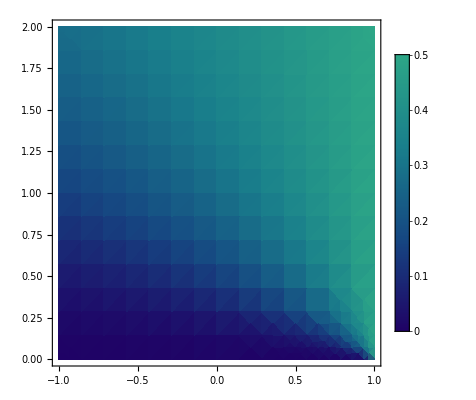
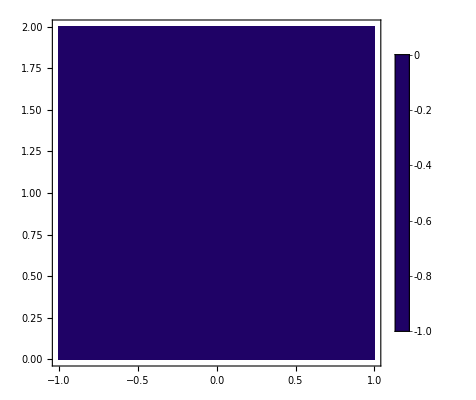
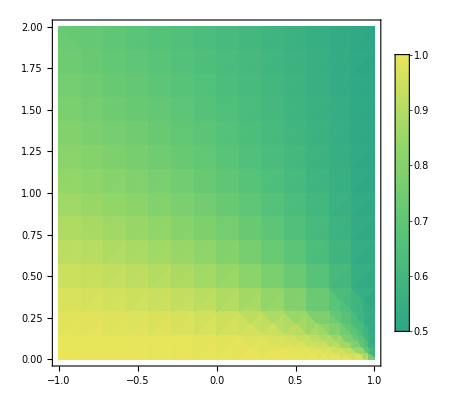
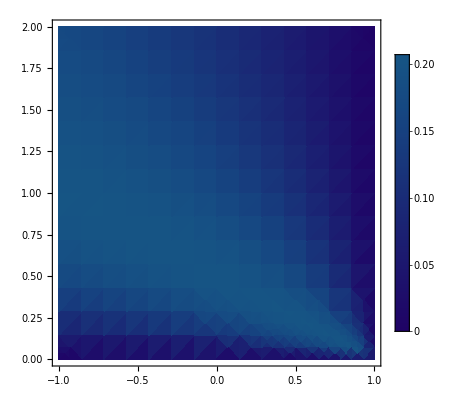

```mathematica
{DensityPlot[DLDrh[Rr,m,1,m],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0,1}]]&),LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],DensityPlot[DLDmh[Rr,m,1,m],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0,1}]]&),LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],DensityPlot[DLDre[Rr,m,1,m],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0,1}]]&),LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],DensityPlot[DLDme[Rr,m,1,m],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0,1}]]&),LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}]}
```

Equation for equal sensitivity to rh and mh (in absolute valu)

```mathematica
Solve[-DLDmh[rho,m,1,m]==DLDrh[rho,m,1,m],m]
```

{{m→1-rho}}

Optimal strategies

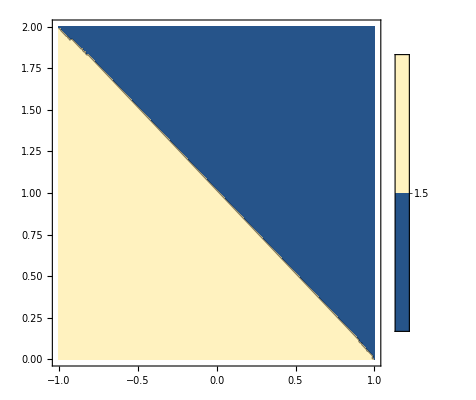

```mathematica
ContourPlot[Position[Abs[{DLDrh[Rr,m,1,m],DLDmh[Rr,m,1,m],DLDme[Rr,m,1,m]}],Max[Abs[{DLDrh[Rr,m,1,m],DLDmh[Rr,m,1,m],DLDme[Rr,m,1,m]}]]][[1,1]],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,Contours->{1.5,2.5,3.5},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}]
```

Figure 1 panel C

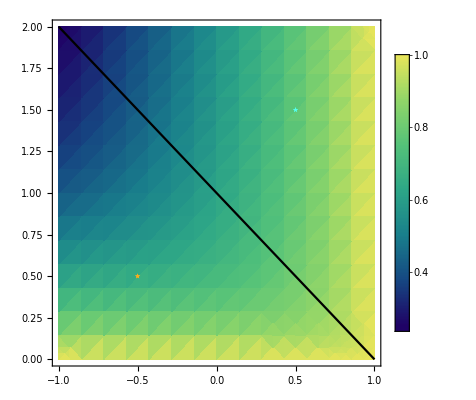

```mathematica
Show[DensityPlot[Lambdaratio[Rr,m],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.25,1}]]&),LabelStyle->{FontSize->20,FontFamily->"Arial",Black}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],ListPlot[{{0.5,1.5}},PlotMarkers->{Style[★,Large,RGBColor[0.33, 1., 0.92]]},PlotStyle->PointSize[Large]],ListPlot[{{-0.5,0.5}},PlotMarkers->{Style[★,Large,RGBColor[1., 0.68, 0.1]]},PlotStyle->PointSize[Large]]]
```

## Asymmetric migration rates (supplementary figure 1)

Analytic expressions for the possible contours

```mathematica
Solve[-DLDmh[rho,a*m,1,m]==DLDrh[rho,a*m,1,m],m]
```

{{m→(1-rho)/a}}

```mathematica
Solve[DLDme[rho,a*m,1,m]==DLDrh[rho,a*m,1,m],m]
```

{{m→0},{m→-(2 (-1+rho))/(2+a)}}

```mathematica
Solve[DLDme[rho,a*m,1,m]==-DLDmh[rho,a*m,1,m],m]
```

{{m→(1-rho)/(2 (-1+a))}}

Optimal strategies - superposed with possible contours

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

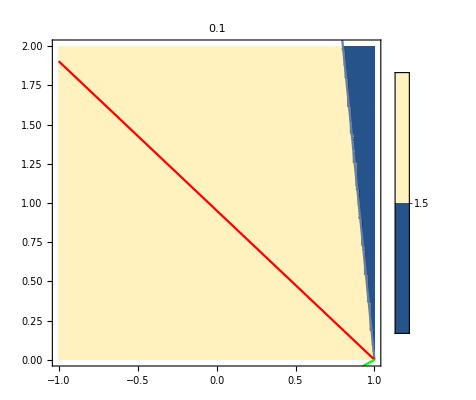
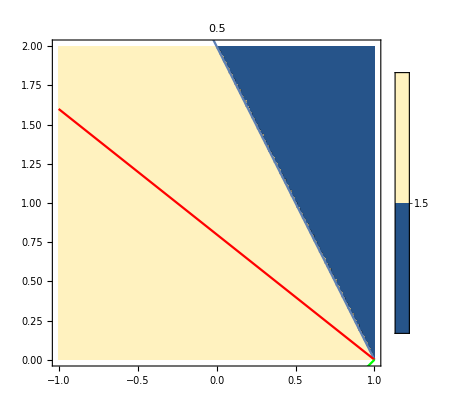
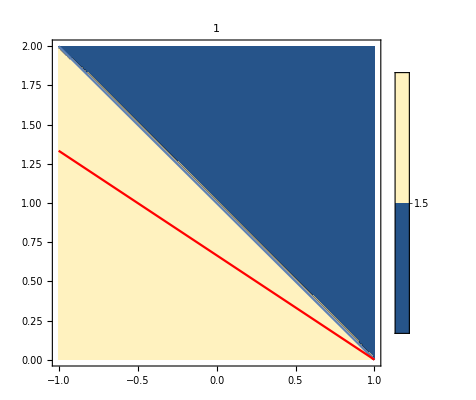
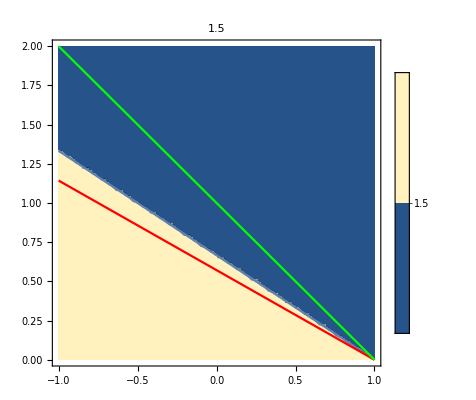
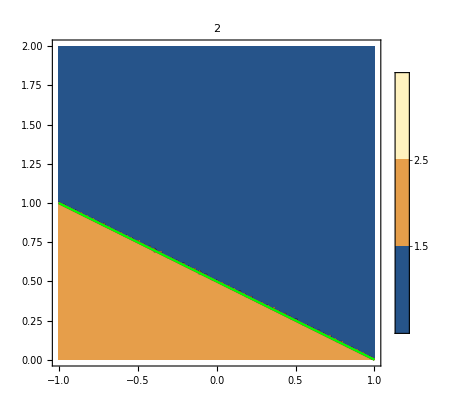
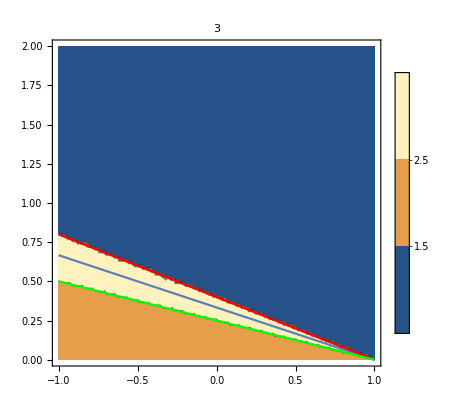
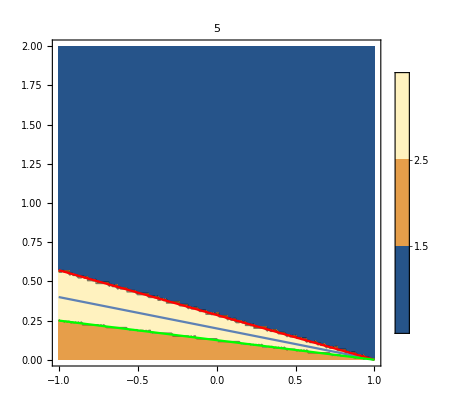
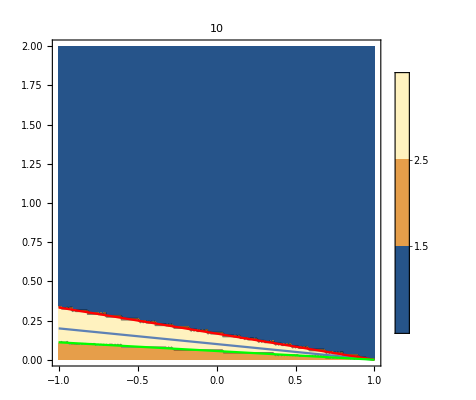

```mathematica
α={0.1,0.5,1,1.5,2,3,5,10};
Table[Show[ContourPlot[Position[Abs[{DLDrh[Rr,α[[ia]]*m,1,m],DLDmh[Rr,α[[ia]]*m,1,m],DLDme[Rr,α[[ia]]*m,1,m]}],Max[Abs[{DLDrh[Rr,α[[ia]]*m,1,m],DLDmh[Rr,α[[ia]]*m,1,m],DLDme[Rr,α[[ia]]*m,1,m]}]]][[1,1]],{Rr,-1,1},{m,0,2},PlotLegends->Automatic,Contours->{1.5,2.5,3.5},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold},PlotLabel->α[[ia]]],Plot[(1-rho)/α[[ia]],{rho,-1,1}],Plot[-(2 (-1+rho))/(2+α[[ia]]),{rho,-1,1},PlotStyle->Red],Plot[(1-rho)/(2 (-1+α[[ia]])),{rho,-1,1},PlotStyle->Green]],{ia,1,Length[α]}]
```

Supplementary figure 1

```mathematica
α={0.1,0.5,1,1.5,2}
```

{0.1,0.5,1,1.5,2}

```mathematica
α2={5,10}
```

{5,10}

```mathematica
Alpha=Flatten[{α,α2}]
```

{0.1,0.5,1,1.5,2,5,10}

```mathematica
listcolor=Table[ColorData["Rainbow"][k],{k,0,1,1/(Length[Alpha]-1)}]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.246296, 0.31595666666666666, 0.80044],RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.901627, 0.5398719999999999, 0.208366],RGBColor[0.857359, 0.131106, 0.132128]}

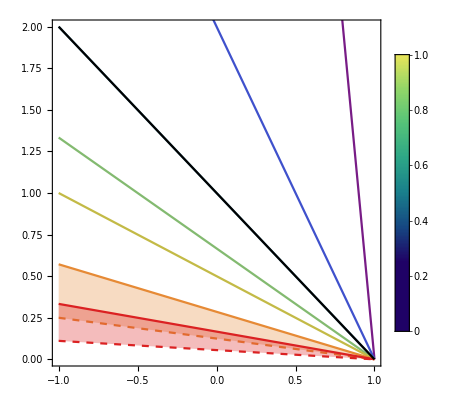

```mathematica
Show[DensityPlot[,{Rr,-1,1},{m,0,2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.25,1}]]&),LabelStyle->{FontSize->20,FontFamily->"Arial",Black}],Table[Plot[(1-rho)/α[[ia]],{rho,-1,1},PlotStyle->Directive[listcolor[[ia]],Opacity[1]]],{ia,1,Length[α]}],Table[Plot[{-(2 (-1+rho))/(2+α2[[ia2]]),(1-rho)/(2 (-1+α2[[ia2]]))},{rho,-1,1},PlotStyle->{listcolor[[Length[α]+ia2]],Directive[listcolor[[Length[α]+ia2]],Dashed,Opacity[1]]},Filling->{1->{2}},FillingStyle->Directive[listcolor[[Length[α]+ia2]],Opacity[0.3]]],{ia2,1,Length[α2]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],PlotRange->{{-1,1},{0,2}},AspectRatio->1,Frame->True]
```